```mathematica
ω0=2.356*10^15
```

2.356×10^15

```mathematica
"velocity of reflecting electron sheath in units of c"
```

velocity of reflecting electron sheath in units of c

```mathematica
β=(-0.014)
```

-0.014

```mathematica
"dopplershift for redshifted gives relative number"
doppler = 1-(1+β)/(1-β)
```

dopplershift for redshifted gives relative number

0.0276134

```mathematica
c=3*10^8
```

300000000

```mathematica
"number of laser cycles for tL=20fs"
```

number of laser cycles for tL=20fs

```mathematica
m =9
```

9

```mathematica
"attemp to introduce quadratic depency ... (wo-w)**2 IS WRONG
J = ∑_(k = 1)^m Cos[2*π*k*ω]*ⅇ^(ⅈ*2*π*C1*(ω + 1 - SuperscriptBox[ω, 2]))*ⅇ^(ⅈ*2*π*SuperscriptBox[k, 2]*(ω (β))/m);

phi =-C1*(ω-ω0)^2;
C1 = (beta/4)/(0.05+beta^2);

beta = (1/(900*10^-15)^2)/(ω0/2*π)^2;
N[C1];

Iw=ω^(-8/3)* Abs[J]^2;"
```

attemp to introduce quadratic depency ... (wo-w)**2 IS WRONG
J = ∑_(k = 1)^m Cos[2*π*k*ω]*ⅇ^(ⅈ*2*π*C1*(ω + 1 - SuperscriptBox[ω, 2]))*ⅇ^(ⅈ*2*π*SuperscriptBox[k, 2]*(ω (β))/m);

phi =-C1*(ω-ω0)^2;
C1 = (beta/4)/(0.05+beta^2);

beta = (1/(900*10^-15)^2)/(ω0/2*π)^2;
N[C1];

Iw=ω^(-8/3)* Abs[J]^2;

```mathematica
"original equation from Daniel von der Bruegge PHD thesis, except the sign of beta"
" beta might origin from the doppler shift calculation relative shift is ∂ω = ω2/ω0, meaning ω2 = ∂ω *ω0 "
J2 = ∑_(k=1)^m (1/m)*(Cos[2*π*k*ω]*ⅇ^(ⅈ*2*π*k^2*(ω)*(β)/(m)));
Iw2 =ω^(-8/3)* Abs[J2]^2;

 "GVD in fs^2 units"

GVD =500;

"chirped pulse duration"
tChirped = √(tl^4+16*0.69^2*GVD^2)/tl;
"compressed pulse  duration"
tl=20;

"Number of laser cycles for chirped pulse"
numberCycles = tChirped/2.671

"laser bandwidth in 10^15 s"

bandwidth = 0.24;

"(w0 - bandwidth)/w0"

shiftperpulse = ((bandwidth*10^15))/ω0

"i am not so sure if this has to be separated into fractions per laser cycle"


"relativeShift "
relativeShift=(shiftperpulse)/(tl/2.671)-((shiftperpulse)/(numberCycles))
```

original equation from Daniel von der Bruegge PHD thesis, except the sign of beta

beta might origin from the doppler shift calculation relative shift is ∂ω = ω2/ω0, meaning ω2 = ∂ω *ω0

GVD in fs^2 units

chirped pulse duration

compressed pulse  duration

Number of laser cycles for chirped pulse

26.8963

laser bandwidth in 10^15 s

(w0 - bandwidth)/w0

0.101868

i am not so sure if this has to be separated into fractions per laser cycle

relativeShift

0.009817

print relativeShift by GVD

0.009817

print orginal surface velocity parameter beta

-0.014

difference beta and GVD shift parameter

-0.004183

calculation to compensate frequency shift from surface movement by GVD shift

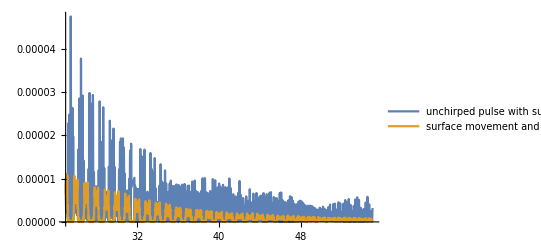

```mathematica
"print relativeShift by GVD"
relativeShift

"print orginal surface velocity parameter beta"
β

"difference beta and GVD shift parameter"
N[β+relativeShift]

"calculation to compensate frequency shift from surface movement by GVD shift"
J3 = ∑_(k=1)^numberCycles (1/(numberCycles))*(Cos[2*π*k*ω]*ⅇ^(-ⅈ*2*π*k^2*ω*(β+relativeShift)/(numberCycles)));
Iw3=ω^(-8/3)* Abs[J3]^2;

Plot[{  Iw2, Iw3},{ω,25,55},PlotRange->Full, PlotLegends->{"unchirped pulse with surface movement", "surface movement and GVD"}]
```

```mathematica
"calculation via denting: maximum denting -> surface velocity for whole pulse"
```

calculation via denting: maximum denting -> surface velocity for whole pulse

```mathematica
denting =20*10^-9;
N[denting]

"GVD was... :"
GVD
```

2.×10^-8

GVD was... :

500

```mathematica
"velocity by denting for compressed pulse"
vbyDentingNoGVD = (denting/(0.5*tl*10^-15))

"velocity by denting for chirped pulse"
vbyDenting = (denting/(0.5*tChirped*10^-15))

β = vbyDentingNoGVD/c;
β1=vbyDenting/c;

"calculation: Δω = w2-w0 , ∂w = Δw/w0 (compressed, chirped)"
relshiftNoGVD = (ω0-((1+β)/(1-β))*ω0 )/ω0
relativeShiftdenting = (ω0-((1+β1)/(1-β1))*ω0 )/ω0


"dopplershift by dentingvelocity Δω = w2-w0 , ∂w = Δw/w0 , w2=((1+β)/(1-β))*ω0 "
N[(ω0-((1+β)/(1-β))*ω0 )/ω0]

"compare to δw=((1+β)/(1-β))"
N[1-((1+β)/(1-β))]


α= relativeShiftdenting;
βdenting = relshiftNoGVD ;

"relative shift denting per cycle for chirped pulse"
N[α]

"relative shift denting per cycle for compressed pulse"
N[βdenting]



" relative shift per cycle from GVD correction"
N[relativeShift/4]




J4 = ∑_(k=1)^numberCycles (1/(numberCycles))*(Cos[2*π*k*ω]*ⅇ^(-ⅈ*2*π*k^2*ω*(α+relativeShift/4)/(numberCycles)));
Iw4=ω^(-8/3)* Abs[J4]^2;



J5= ∑_(k=1)^9 (1/(9))*(Cos[2*π*k*ω]*ⅇ^(ⅈ*2*π*k^2*ω*(βdenting)/(9)));
Iw5=ω^(-8/3)* Abs[J5]^2;

"approach for  quadratic phase term"

J6= ∑_(k=1)^numberCycles (1/(numberCycles))*(Cos[2*π*k*ω]*ⅇ^(ⅈ*2*π*k^2*ω*(α)/(numberCycles)));
Iw6=ω^(-8/3)* Abs[J6]^2;
```

velocity by denting for compressed pulse

2.×10^6

velocity by denting for chirped pulse

556792.

calculation: Δω = w2-w0 , ∂w = Δw/w0 (compressed, chirped)

-0.0134228

-0.00371885

dopplershift by dentingvelocity Δω = w2-w0 , ∂w = Δw/w0 , w2=((1+β)/(1-β))*ω0

-0.0134228

compare to δw=((1+β)/(1-β))

-0.0134228

relative shift denting per cycle for chirped pulse

-0.00371885

relative shift denting per cycle for compressed pulse

-0.0134228

relative shift per cycle from GVD correction

0.00245425

approach for  quadratic phase term

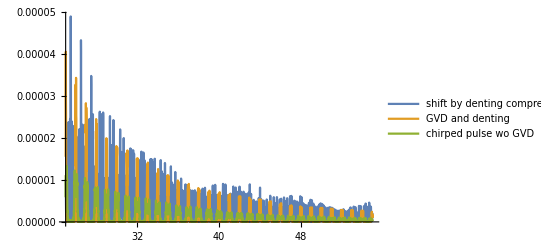

```mathematica
Plot[{  Iw5, Iw4, Iw6},{ω,25,55},PlotRange->Full, PlotLegends->{ "shift by denting compressed pulse","GVD and denting", "longer pulse duration"}]
```